# Initialization

## Generalities

```mathematica
(* Kronecker delta *)
SetAttributes[δ,Orderless]

(* replace Kronecker deltas (use with /. and not with //. *)
aSum:=((expr_. δ[a_,i_]):>If[a===i,expr N,expr/.a->i])
```

```mathematica
(* mediating function with delayed behavior of OddQ *)
oddQ[n_?NumericQ]:=OddQ[n]
```

```mathematica
(* R-symmetry inner product *)
RProduct[ϕϕ1_,ϕϕ2_]:=If[MemberQ[{Z^2,(Z̄)^2,X^2,(X̄)^2,Z X,Z X̄,Z̄ X,Z̄ X̄},ϕϕ1 ϕϕ2],0,Subscript[u, ϕϕ1 ϕϕ2]]

(* scalar propagator, save for gauge indices *)
propagatorStandard[ϕ1_[x1_],ϕ2_[x2_]]:=1/(2N)II[{x1,x2}//Sort]RProduct[ϕ1,ϕ2]

(* connected part of indexless product (LO contractions between list1 and list2) x (LO contractions between list3 and list4) *)
contractionFree[list1_,list2_,list3_,list4_,max1OverN_]:=
Module[{output},
If[Length[list1]≠Length[list2]||Length[list3]≠Length[list4],output=0,{

If[Length[list1]==0&&Length[list3]==0,
output=1;
];

If[Length[list1]≠0&&Length[list3]==0,
perm=Permutations[list2];
switch=Select[Tuples[{0,1},Length[list1]],(Count[#,1]≤max1OverN)&];

output=Sum[If[ConnectedGraphQ[Graph[Table[list1[[index]]<->perm[[indexperm,index]],{index,Length[list1]}]/.{Subscript[ϕ_[x__], i_,j_]:>x}//Flatten]],graphSpacetime[Table[list1[[index]]<->perm[[indexperm,index]],{index,Length[list1]}]/.{Subscript[ϕ_[x__], i_,j_]:>x}//Flatten]Product[propagator[list1[[index]]/.{Subscript[ϕ_[x__], i_,j_]:>ϕ[x]},perm[[indexperm,index]]/.{Subscript[ϕ_[x__], i_,j_]:>ϕ[x]}],{index,Length[list1]}]Sum[(-1/N)^Count[switch[[indexSwitch]],1] Power[N,Length[ConnectedComponents[Graph[Table[{{(list1[[index]]/.{Subscript[ϕ_[x__], i_,j_]:>i})<->If[switch[[indexSwitch,index]]==0,perm[[indexperm,index]]/.{Subscript[ϕ_[x__], i_,j_]:>j},list1[[index]]/.{Subscript[ϕ_[x__], i_,j_]:>j}]}, {(perm[[indexperm,index]]/.{Subscript[ϕ_[x__], i_,j_]:>i})<->If[switch[[indexSwitch,index]]==0,(list1[[index]]/.{Subscript[ϕ_[x__], i_,j_]:>j}),perm[[indexperm,index]]/.{Subscript[ϕ_[x__], i_,j_]:>j}]}},{index,Length[list1]}]//Flatten]]]],{indexSwitch,Length[switch]}],0],{indexperm,Length[perm]}];
];

If[Length[list1]==0&&Length[list3]≠0,
output=contractionFree[list3,list4,list1,list2,max1OverN];
];

If[Length[list1]≠0&&Length[list3]≠0,{
perm2=Permutations[list2];
perm4=Permutations[list4];
switch1=Select[Tuples[{0,1},Length[list1]],(Count[#,1]≤max1OverN)&];
switch3=Select[Tuples[{0,1},Length[list3]],(Count[#,1]≤max1OverN)&];

output=Sum[If[ConnectedGraphQ[Graph[Join[Table[list1[[index1]]<->perm2[[indexperm2,index1]],{index1,Length[list1]}],Table[list3[[index3]]<->perm4[[indexperm4,index3]],{index3,Length[list3]}]]/.{Subscript[ϕ_[x__], i_,j_]:>x}//Flatten]],graphSpacetime[Join[Table[list1[[index1]]<->perm2[[indexperm2,index1]],{index1,Length[list1]}],Table[list3[[index3]]<->perm4[[indexperm4,index3]],{index3,Length[list3]}]]/.{Subscript[ϕ_[x__], i_,j_]:>x}//Flatten]Product[propagator[list1[[index1]]/.{Subscript[ϕ_[x__], i_,j_]:>ϕ[x]},perm2[[indexperm2,index1]]/.{Subscript[ϕ_[x__], i_,j_]:>ϕ[x]}],{index1,Length[list1]}]Product[propagator[list3[[index3]]/.{Subscript[ϕ_[x__], i_,j_]:>ϕ[x]},perm4[[indexperm4,index3]]/.{Subscript[ϕ_[x__], i_,j_]:>ϕ[x]}],{index3,Length[list3]}]Sum[(-1/N)^(Count[switch1[[indexswitch1]],1]+Count[switch3[[indexswitch3]],1])Power[N,Length[ConnectedComponents[Graph[Join[Table[{{(list1[[index1]]/.{Subscript[ϕ_[x__], i_,j_]:>i})<->If[switch1[[indexswitch1,index1]]==0,perm2[[indexperm2,index1]]/.{Subscript[ϕ_[x__], i_,j_]:>j},list1[[index1]]/.{Subscript[ϕ_[x__], i_,j_]:>j}]}, {(perm2[[indexperm2,index1]]/.{Subscript[ϕ_[x__], i_,j_]:>i})<->If[switch1[[indexswitch1,index1]]==0,(list1[[index1]]/.{Subscript[ϕ_[x__], i_,j_]:>j}),perm2[[indexperm2,index1]]/.{Subscript[ϕ_[x__], i_,j_]:>j}]}},{index1,Length[list1]}],Table[{{(list3[[index3]]/.{Subscript[ϕ_[x__], i_,j_]:>i})<->If[switch3[[indexswitch3,index3]]==0,perm4[[indexperm4,index3]]/.{Subscript[ϕ_[x__], i_,j_]:>j},list3[[index3]]/.{Subscript[ϕ_[x__], i_,j_]:>j}]}, {(perm4[[indexperm4,index3]]/.{Subscript[ϕ_[x__], i_,j_]:>i})<->If[switch3[[indexswitch3,index3]]==0,(list3[[index3]]/.{Subscript[ϕ_[x__], i_,j_]:>j}),perm4[[indexperm4,index3]]/.{Subscript[ϕ_[x__], i_,j_]:>j}]}},{index3,Length[list3]}]]//Flatten]]]],{indexswitch1,Length[switch1]},{indexswitch3,Length[switch3]}],0],{indexperm2,Length[perm2]},{indexperm4,Length[perm4]}];

}];

}];

output

]

(* vertices *)
vertexX[V_,doubleTraceVertices_]:=Module[{output},
If[V==0,output=1,{

indexgauge=1000; (* hardcoded offset *)
output=0;

For[V1=0,V1≤V,V1++,
For[V2=0,V2≤V,V2++,
For[V3=0,V3≤V,V3++,
For[V4=0,V4≤V,V4++,

V5=V-V1-V2-V3-V4;

If[V5<0,Break[]];

If[doubleTraceVertices||((!doubleTraceVertices)&&(V1==V)),{
tmp=1;
indexpt=1;

Do[{
tmp=tmp(4π)^2 ξ^2 N contractionFreeHold[{Subscript[X̄[x[indexpt]], m[indexgauge],m[indexgauge+1]],Subscript[Z̄[x[indexpt]], m[indexgauge+1],m[indexgauge+2]],Subscript[X[x[indexpt]], m[indexgauge+2],m[indexgauge+3]],Subscript[Z[x[indexpt]], m[indexgauge+3],m[indexgauge]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V1];
}];

If[doubleTraceVertices,{
Do[{
tmp=tmp(4π)^2 α1^2 contractionFreeHold[{Subscript[X[x[indexpt]], m[indexgauge],m[indexgauge+1]],Subscript[X[x[indexpt]], m[indexgauge+1],m[indexgauge]],Subscript[X̄[x[indexpt]], m[indexgauge+2],m[indexgauge+3]],Subscript[X̄[x[indexpt]], m[indexgauge+3],m[indexgauge+2]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V2];
Do[{
tmp=tmp(4π)^2 α1^2 contractionFreeHold[{Subscript[Z[x[indexpt]], m[indexgauge],m[indexgauge+1]],Subscript[Z[x[indexpt]], m[indexgauge+1],m[indexgauge]],Subscript[Z̄[x[indexpt]], m[indexgauge+2],m[indexgauge+3]],Subscript[Z̄[x[indexpt]], m[indexgauge+3],m[indexgauge+2]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V3];
Do[{
tmp=-tmp(4π)^2 α2^2 contractionFreeHold[{Subscript[X[x[indexpt]], m[indexgauge],m[indexgauge+1]],Subscript[Z[x[indexpt]], m[indexgauge+1],m[indexgauge]],Subscript[X̄[x[indexpt]], m[indexgauge+2],m[indexgauge+3]],Subscript[Z̄[x[indexpt]], m[indexgauge+3],m[indexgauge+2]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V4];
Do[{
tmp=-tmp(4π)^2 α2^2 contractionFreeHold[{Subscript[X[x[indexpt]], m[indexgauge],m[indexgauge+1]],Subscript[Z̄[x[indexpt]], m[indexgauge+1],m[indexgauge]],Subscript[Z[x[indexpt]], m[indexgauge+2],m[indexgauge+3]],Subscript[X̄[x[indexpt]], m[indexgauge+3],m[indexgauge+2]]}];
indexpt=indexpt+1;
indexgauge=indexgauge+4;
},V5];

}];

If[doubleTraceVertices||((!doubleTraceVertices)&&(V1==V)),
output=output+(-1)^V/(V1!V2!V3!V4!V5!)tmp;
];

]]]];

}];

output

]
```

```mathematica
(* PCGG before multitrace expansion *)
```

```mathematica
PCGGPref[L_]:=((N-L/2)!)/((L/2)!)^2(1/2 1/N II[{x1,x2}] Subscript[u, ϕ1 ϕ2])^(N-L/2)
PCGGDelta[L_,0]:=If[L==0,1,Det[Table[δ[i[ii],ll[iii]],{ii,L/2},{iii,L/2}]]Det[Table[δ[j[ii],k[iii]],{ii,L/2},{iii,L/2}]]]
PCGGDelta[L_,1]:=(-1/N)^1 Binomial[N-L/2,1](((N-L/2-1)!)/((N-L/2)!))^2 δ[i[L/2+1],j[L/2+1]]δ[k[L/2+1],ll[L/2+1]]Det[Table[δ[i[ii],ll[iii]],{ii,L/2+1},{iii,L/2+1}]]Det[Table[δ[j[ii],k[iii]],{ii,L/2+1},{iii,L/2+1}]]
PCGGDelta[L_,2]:=(-1/N)^2 Binomial[N-L/2,2](((N-L/2-2)!)/((N-L/2)!))^2 δ[i[L/2+1],j[L/2+1]]δ[k[L/2+1],ll[L/2+1]]δ[i[L/2+2],j[L/2+2]]δ[k[L/2+2],ll[L/2+2]]Det[Table[δ[i[ii],ll[iii]],{ii,L/2+2},{iii,L/2+2}]]Det[Table[δ[j[ii],k[iii]],{ii,L/2+2},{iii,L/2+2}]]
PCGGMatrix[L_]:=If[L==0,1,contractionFreeHold[Join[Table[Subscript[ϕ1[x1], i[ii],j[ii]],{ii,L/2}],Table[Subscript[ϕ2[x2], k[ii],ll[ii]],{ii,L/2}]]]]
```

```mathematica
(* determinants *)
det1Matrix[N_]:=Table[Subscript[ϕ1[x1], i1[ii],j1[ii]],{ii,N}]
det2Matrix[N_]:=Table[Subscript[ϕ2[x2], i2[ii],j2[ii]],{ii,N}]

det1Delta[N_]:=1/(N!)Det[Table[δ[i1[ii],j1[iii]],{ii,N},{iii,N}]]
det2Delta[N_]:=1/(N!)Det[Table[δ[i2[ii],j2[iii]],{ii,N},{iii,N}]]
```

```mathematica
(* 3-pt function: vacuum *)

vacuum[L_]:=If[L==0,{},Table[Subscript[ϕ3[x3], o[ii],o[ii+1]],{ii,L}]/.{o[L+1]->o[1]}//Flatten]
```

```mathematica
(* couplings *)
couplings=Flatten[{{α1->√(pm(ⅈ ξ^2)/2-ξ^4/2-pm(3ⅈ ξ^6)/4+ξ^8+pm(65 ⅈ ξ^10)/48-(19 ξ^12)/10+unk ξ^14)}, {α2->ξ}, {pm^n_:>If[EvenQ[n],1,pm^n]}, {pm^n_:>If[OddQ[n],pm,pm^n]}}];
```

## Convert lists into product of traces and vice versa

```mathematica
listToTraces[list__]:=
Module[{output},

field[Subscript[A_, x_,y_]]:=A;
index1[Subscript[A_, x_,y_]]:=x;
index2[Subscript[A_, x_,y_]]:=y;

input=list;
indices=Table[index1[input[[dummyindex]]],{dummyindex,Length[input]}];
output=1;

While[input!={},{

currentPosition=1;
bucket={};

While[True,{

(* add matrix in input to temporary list *)
AppendTo[bucket,input[[currentPosition]]];
(* find next matrix in input *)
nextPosition=Position[indices,index2[input[[currentPosition]]]][[1,1]];

If[nextPosition==1,{
(* the next matrix is the first one because the trace is complete *)
Table[{{indices=DeleteCases[indices,index1[bucket[[dummyindex]]]]}, {input=DeleteCases[input,bucket[[dummyindex]]]}},{dummyindex,Length[bucket]}];
output=output tr[bucket];
bucket={};
currentPosition=1;

(* if this was the last trace to find, the algorithm terminates *)
If[input=={},Break[]];
},{
(* the next matrix is new, so the trace is not complete yet *)
currentPosition=nextPosition;
}];

}];
}];

output=output/.{Subscript[A_, x_,y_]:>A}
]
```

```mathematica
tracesToList[traces__]:=
Module[{output},

(* list of traces and their powers *)
input=DeleteCases[traces//FactorList,{1,1}];
(* initialize output list *)
output={};

(* counter for matrix indices *)
indexCount=1;

For[indexOverTraces=1,indexOverTraces≤Length[input],indexOverTraces++,{
(* for each trace type *)

Do[{
(* repeat a number of times equal to the trace power *)

(* remember first index to close the trace later *)
indexFirstMatrix=indexCount;

For[indexInTrace=1,indexInTrace≤Length[input[[indexOverTraces,1]][[1]]],indexInTrace++,{
(* add fields to output list *)
AppendTo[output,Subscript[(input[[indexOverTraces,1]][[1]][[indexInTrace]]), q[indexCount],q[indexCount+1]]];
indexCount=indexCount+1;
}];

(* close the trace *)
output=output/.{q[indexCount]->q[indexFirstMatrix]};
indexCount=indexCount+1;

},input[[indexOverTraces,2]]];


}];

output
]
```

```mathematica
(* example *)

tr[{Z[X1],Z̄[X2]}]^2 tr[{Z[X1],Z̄[X2],Z̄[X2]}]^3 tr[{Z[X1],Z̄[X2],Z[X1],Z̄[X2]}];
tracesToList[%]
listToTraces[%]==%%
```

{Z[X1]_(q[1],q[2]),(Z̄[X2])_(q[2],q[1]),Z[X1]_(q[4],q[5]),(Z̄[X2])_(q[5],q[4]),Z[X1]_(q[7],q[8]),(Z̄[X2])_(q[8],q[9]),(Z̄[X2])_(q[9],q[7]),Z[X1]_(q[11],q[12]),(Z̄[X2])_(q[12],q[13]),(Z̄[X2])_(q[13],q[11]),Z[X1]_(q[15],q[16]),(Z̄[X2])_(q[16],q[17]),(Z̄[X2])_(q[17],q[15]),Z[X1]_(q[19],q[20]),(Z̄[X2])_(q[20],q[21]),Z[X1]_(q[21],q[22]),(Z̄[X2])_(q[22],q[19])}

True

## Cyclically permute scalars in trace to reach a conventional ordering

```mathematica
orderTrace[list_]:=
Module[{output},

If[Length[list]==0,
output={},
output=SortBy[NestList[RotateRight,list,Length[list]-1],Last][[1]]
];

output

]
```

```mathematica
(* test *)

RandomInteger[{1,4},5];
NestList[RotateRight,%,Length[%]-1];
tr@@@%;
%/.{tr[expr__]:>tr[orderTrace[{expr}]]};
Length[Union[%]]==1
```

True

# <GG GG> tree-level

```mathematica
propagator=propagatorStandard;

fit[N_]:=1/(N!)(1/(2N)II[{x1,x2}](Subscript[u, Z Z̄]+Subscript[u, X X̄]))^N((N+(-1/N)^N ) (N!)^2)/(N+1)

NN=4;

det1Delta[NN]det2Delta[NN]contractionFreeHold[Join[det1Matrix[NN],det2Matrix[NN]]]/.{ϕ1->Z+X,ϕ2->Z̄+X̄}/.N->NN;
tmp=%//Expand;

(* write tree-level PCGG in traces... *)
tmp2=0;
While[tmp=!=tmp2,{
tmp2=tmp;
tmp=tmp//.{δ[i_,j_] δ[k_,j_]:>δ[i,k]}//.{δ[i_,i_] :>N}//.{δ[i_,j_]^n_:>If[n==2,N^(n/2),∞]}/.aSum;
}];

tmp/.{contractionFreeHold[list_]:>contractionFreeHold[listToTraces[list]]};
(* ... enforce tracelessness... *)
%/.{tr[list_]:>If[Length[list]==1,0,tr[list]]}/.{contractionFreeHold[0]->0};
(* ... and go back to indices, but with fewer terms now *)
%/.{contractionFreeHold[traces_]:>contractionFreeHold[tracesToList[traces]]}/.{q[n_]:>i[n]};

(* if ϕ1 or ϕ2 are sums, then distribute R-symmetry products over them *)
%/.{ϕ1->Z+X,ϕ2->Z̄+X̄}//.{Subscript[(ϕϕ1_+ϕϕ2_)[x_], i_,j_]:>Subscript[ϕϕ1[x], i,j]+Subscript[ϕϕ2[x], i,j]}//.{Subscript[(-ϕϕ1_)[x_], i_,j_]:>-Subscript[ϕϕ1[x], i,j]}/.{contractionFreeHold[list_]:>contractionFreeHold[list//.{{x__}:>x}]}//.{contractionFreeHold[x__]:>Distribute[contractionFreeHold[x]]};
%/.{contractionFreeHold[-x_,y_]:>-contractionFreeHold[x,y],contractionFreeHold[x_,-y_]:>-contractionFreeHold[x,y]};
%/.{contractionFreeHold[x__]:>contractionFreeHold[{x}]}//Expand;

(* one contractionFreeHold per addend *)
%//.{contractionFreeHold[list1_]contractionFreeHold[list2_]:>contractionFreeHold[Join[list1,list2]]};

(* split into products of Z,Z̄ and products of X,X̄ *)
%//.{contractionFreeHold[list_]:>contractionFreeHold[Cases[list,Subscript[Z[x__], i__,j__]],Cases[list,Subscript[Z̄[x__], i__,j__]],Cases[list,Subscript[X[x__], i__,j__]],Cases[list,Subscript[X̄[x__], i__,j__]]]};

(* Wick contractions *)
%//.{contractionFreeHold[list1_,list2_,list3_,list4_]:>contractionFree[list1,list2,list3,list4,∞]}/.{graphSpacetime[list_]->1};

%-fit[NN]/.{N->NN}//Expand

Clear[NN,propagator,tmp,tmp2,fit]
```

0

# Save tree-level PCGG made of terms n=0,1,2

```mathematica
Lp=4;

EvenQ[Lp]&&(Lp≥2)

tmp=(PCGGDelta[Lp,0]+ A PCGGDelta[Lp,1]+B PCGGDelta[Lp,2])PCGGMatrix[Lp]//.{(n_+N)!:>((1+n+N)!)/(1+n+N)}//Expand;

(* write tree-level PCGG in traces... *)
tmp2=0;
While[tmp=!=tmp2,{
tmp2=tmp;
tmp=tmp//.{δ[i_,j_] δ[k_,j_]:>δ[i,k]}//.{δ[i_,i_] :>N}//.{δ[i_,j_]^n_:>If[n==2,N^(n/2),∞]}/.aSum;
}];
tmp/.{contractionFreeHold[list_]:>contractionFreeHold[listToTraces[list]]};
(* ... enforce tracelessness... *)
%/.{tr[list_]:>If[Length[list]==1,0,tr[list]]};
%/.{contractionFreeHold[0]->0}//Collect[#,contractionFreeHold[expr_],Simplify]&;
(* ... order scalars in traces... *)
%/.{tr[expr__]:>tr[orderTrace[expr]]};
%//Collect[#,contractionFreeHold[expr_],Simplify]&;
(* ... and go back to indices, but with fewer terms now *)
%//Collect[#,contractionFreeHold[expr_],Simplify]&;
%/.{contractionFreeHold[traces_]:>contractionFreeHold[tracesToList[traces]]}/.{q[n_]:>i[n]};

PCGGDeltaAB[Lp]=%

Clear[tmp]
```

True

(2 B contractionFreeHold[{ϕ1[x1]_(i[1],i[2]),ϕ1[x1]_(i[2],i[1]),ϕ2[x2]_(i[4],i[5]),ϕ2[x2]_(i[5],i[4])}])/(N^2 (6-5 N+N^2))+((8 B (-4+N)-4 A (-3+N) N) contractionFreeHold[{ϕ1[x1]_(i[1],i[2]),ϕ2[x2]_(i[2],i[3]),ϕ2[x2]_(i[3],i[4]),ϕ1[x1]_(i[4],i[1])}])/((-3+N) (-2+N) N^2)+(2 ((-3+N) N (-A (-4+N)+(-2+N) N)+B (20-9 N+N^2)) contractionFreeHold[{ϕ2[x2]_(i[1],i[2]),ϕ1[x1]_(i[2],i[1]),ϕ2[x2]_(i[4],i[5]),ϕ1[x1]_(i[5],i[4])}])/((-3+N) (-2+N) N^2)-(2 ((-3+N) N (-A (-4+N)+(-2+N) N)+B (20-9 N+N^2)) contractionFreeHold[{ϕ2[x2]_(i[1],i[2]),ϕ1[x1]_(i[2],i[3]),ϕ2[x2]_(i[3],i[4]),ϕ1[x1]_(i[4],i[1])}])/((-3+N) (-2+N) N^2)

```mathematica
(* save/load for Lp=2,4,6,8 *)
```

```mathematica
(*Save[NotebookDirectory[]<>"PCGGDeltaAB.mx",{PCGGDeltaAB}];
```

```mathematica
(*<<(NotebookDirectory[]<>"PCGGDeltaAB.mx");
```

# <GG GG tr(...)>

```mathematica
propagator[ϕ1_[xx1_],ϕ2_[xx2_]]:=If[Sort[{xx1,xx2}]==={x1,x2},0,propagatorStandard[ϕ1[xx1],ϕ2[xx2]]]

Lp=6;
V=2;
max1OverN=∞;
A=0;
B=0;
doubleTraceVertices=True;

scalartype={Z,Z̄};
scalartype={Z+X̄,Z̄+X};
scalartype={Z̄+X,Z̄+X̄};

scalartype={X+Z,X̄+Z̄};

singletrace={Subscript[Z[x3], o[1],o[2]],Subscript[X[x3], o[2],o[1]]};
singletrace={Subscript[Z[x3], o[1],o[2]],Subscript[X̄[x3], o[2],o[1]]};
singletrace={Subscript[X[x3], o[1],o[2]],Subscript[X̄[x3], o[2],o[1]]};
singletrace={Subscript[Z̄[x3], o[1],o[2]],Subscript[X̄[x3], o[2],o[1]]};
singletrace={Subscript[Z̄[x3], o[1],o[2]],Subscript[X[x3], o[2],o[1]]};
singletrace={Subscript[Z[x3], o[1],o[2]],Subscript[Z̄[x3], o[2],o[1]]};
singletrace={Subscript[Z̄[x3], o[1],o[2]],Subscript[Z̄[x3], o[2],o[1]]};
singletrace={Subscript[Z[x3], o[1],o[2]],Subscript[X̄[x3], o[2],o[1]]};
singletrace={Subscript[Z[x3], o[1],o[2]],Subscript[Z̄[x3], o[2],o[3]],Subscript[Z[x3], o[3],o[4]],Subscript[Z̄[x3], o[4],o[1]]};

singletrace={};
singletrace={Subscript[X[x3], o[1],o[2]],Subscript[Z̄[x3], o[2],o[1]]};

EvenQ[Lp]&&(Lp≥2)&&(V≥0)&&(max1OverN≥0)

(* load tree-level PCGG *)
<<(NotebookDirectory[]<>"PCGGDeltaAB.mx");

(* if ϕ1 or ϕ2 here are sums, then distribute R-symmetry products over them *)
PCGGDeltaAB[Lp]/.{ϕ1->scalartype[[1]],ϕ2->scalartype[[2]]}//.{Subscript[(ϕϕ1_+ϕϕ2_)[x_], i_,j_]:>Subscript[ϕϕ1[x], i,j]+Subscript[ϕϕ2[x], i,j]}//.{Subscript[(-ϕϕ1_)[x_], i_,j_]:>-Subscript[ϕϕ1[x], i,j]}/.{contractionFreeHold[list_]:>contractionFreeHold[list//.{{x__}:>x}]}//.{contractionFreeHold[x__]:>Distribute[contractionFreeHold[x]]};
%/.{contractionFreeHold[-x_,y_]:>-contractionFreeHold[x,y],contractionFreeHold[x_,-y_]:>-contractionFreeHold[x,y]};
%/.{contractionFreeHold[x__]:>contractionFreeHold[{x}]}//Simplify;
(* write in traces... *)
%/.{contractionFreeHold[list_]:>contractionFreeHold[listToTraces[list]]};
%//Collect[#,contractionFreeHold[expr_],Simplify]&;
(* ... order scalars in traces... *)
%/.{tr[expr__]:>tr[orderTrace[expr]]};
%//Collect[#,contractionFreeHold[expr_],Simplify]&;
(* ... and go back to indices, but with fewer terms now *)
%//Collect[#,contractionFreeHold[expr_],Simplify]&;
%/.{contractionFreeHold[traces_]:>contractionFreeHold[tracesToList[traces]]}/.{q[n_]:>i[n]};

(* if scalars in single trace are sums, then distribute R-symmetry products over them *)
contractionFreeHold[singletrace]//.{Subscript[(ϕϕ1_+ϕϕ2_)[x_], i_,j_]:>Subscript[ϕϕ1[x], i,j]+Subscript[ϕϕ2[x], i,j]}//.{Subscript[(-ϕϕ1_)[x_], i_,j_]:>-Subscript[ϕϕ1[x], i,j]}/.{contractionFreeHold[list_]:>contractionFreeHold[list//.{{x__}:>x}]}//.{contractionFreeHold[x__]:>Distribute[contractionFreeHold[x]]};
%/.{contractionFreeHold[-x_,y_]:>-contractionFreeHold[x,y],contractionFreeHold[x_,-y_]:>-contractionFreeHold[x,y]};
%/.{contractionFreeHold[x__]:>If[x==={},contractionFreeHold[{}],contractionFreeHold[{x}]]};
%//Collect[#,contractionFreeHold[expr_],Simplify]&;

(* multiply PCGG and single trace *)
%%%%% %//Expand;
%//Collect[#,contractionFreeHold[expr1_]contractionFreeHold[expr2_],Simplify]&;
(* one contractionFreeHold per addend *)
%//.{contractionFreeHold[list1_]contractionFreeHold[list2_]:>contractionFreeHold[Join[list1,list2]]};
(* write in traces... *)
%/.{contractionFreeHold[list_]:>contractionFreeHold[listToTraces[list]]};
%//Collect[#,contractionFreeHold[expr_],Simplify]&;
(* ... order scalars in traces... *)
%/.{tr[expr__]:>tr[orderTrace[expr]]};
%//Collect[#,contractionFreeHold[expr_],Simplify]&;
(* ... and go back to indices, but with fewer terms now *)
%//Collect[#,contractionFreeHold[expr_],Simplify]&;
%/.{contractionFreeHold[traces_]:>contractionFreeHold[tracesToList[traces]]}/.{q[n_]:>i[n]};

(* insert vertices *)
%/.{contractionFreeHold[list_]:>If[(Count[(list//.{Subscript[ϕ_[x_], i_,j_]:>ϕ,Subscript[ϕ_[x[n_]], i_,j_]:>ϕ}),Z]==Count[(list//.{Subscript[ϕ_[x_], i_,j_]:>ϕ,Subscript[ϕ_[x[n_]], i_,j_]:>ϕ}),Z̄])&&(Count[(list//.{Subscript[ϕ_[x_], i_,j_]:>ϕ,Subscript[ϕ_[x[n_]], i_,j_]:>ϕ}),X]==Count[(list//.{Subscript[ϕ_[x_], i_,j_]:>ϕ,Subscript[ϕ_[x[n_]], i_,j_]:>ϕ}),X̄]),contractionFreeHold2[list],0]};
%/.{contractionFreeHold2[list_]:>vertexX[V,doubleTraceVertices]contractionFreeHold[list]}//Expand;
(* one contractionFreeHold per addend *)
%//.{contractionFreeHold[list1_]contractionFreeHold[list2_]:>contractionFreeHold[Join[list1,list2]]};

(* split into products of Z,Z̄ and products of X,X̄ *)
%//.{contractionFreeHold[list_]:>contractionFreeHold[Cases[list,Subscript[X[x__], i__,j__]],Cases[list,Subscript[X̄[x__], i__,j__]],Cases[list,Subscript[Z[x__], i__,j__]],Cases[list,Subscript[Z̄[x__], i__,j__]]]};

(* Wick contractions *)
tmp=List@@%;
Total[tmp]==%%//Expand

(*time=AbsoluteTime[];*)
Monitor[
Table[tmp[[indexSum]]=(tmp[[indexSum]]//.{contractionFreeHold[list1_,list2_,list3_,list4_]:>contractionFree[list1,list2,list3,list4,max1OverN]}),{indexSum,Length[tmp]}];
,Row[{ProgressIndicator[indexSum,{1,Length[tmp]}],indexSum,"/",Length[tmp]},""]];
(*,Row[{ProgressIndicator[indexSum,{1,Length[tmp]}],indexSum,"/",Length[tmp],If[indexSum>1,", estimated remaining minutes: ",""],If[indexSum>1,N[(1/60(AbsoluteTime[]-time1)/(indexSum-1)(Length[tmp]-indexSum+1))],""]},""]];*)
tmp=Total[tmp];

If[tmp===0,Print["zero"],Print["non-zero"]];
Series[tmp,{N,∞,0}]//Normal;
PCGGPref[Lp]%/.{(n_+N)!:>N^n N!}//PowerExpand//Expand;
%/.{graphSpacetime[list_]:>Graph[list//Sort,VertexLabels->"Name"]}//Simplify
%%/.{graphSpacetime[list_]:>1}//Simplify

(*%/(1/(PCGGPref[Lp]/.{ϕ1->scalartype[[1]],ϕ2->scalartype[[2]]}/.{Subscript[u, (X+Z̄) (X̄+Z̄)]->Subscript[u, X X̄]})((-1)^(Length[singletrace]/2+1)(N-Length[singletrace]/2)!)/(2^(N+Length[singletrace]/2-1)N^(N-Length[singletrace]/2))II[{x1,x2}]^(N-Length[singletrace]/2)(II[{x1,x3}]II[{x2,x3}])^(Length[singletrace]/2)(Subscript[u, X X̄])^(N-Length[singletrace]/2)(Subscript[u, Z Z̄])^Length[singletrace]//PowerExpand)*)
(*%/(1/(PCGGPref[Lp]/.{ϕ1->scalartype[[1]],ϕ2->scalartype[[2]]}/.{Subscript[u, (X+Z̄) (X̄+Z̄)]->Subscript[u, X X̄]})((-1)^(Length[singletrace]/2+1)(N-Length[singletrace]/2)!)/(2^(N+Length[singletrace]/2)N^(N-Length[singletrace]/2))II[{x1,x2}]^(N-Length[singletrace]/2)(II[{x1,x3}]II[{x2,x3}])^(Length[singletrace]/2)(Subscript[u, X X̄])^(N-Length[singletrace]/2+Count[(singletrace//.{Subscript[ϕ_[x__], i_,j_]:>ϕ}),X])(Subscript[u, Z Z̄])^(Length[singletrace]-Count[(singletrace//.{Subscript[ϕ_[x__], i_,j_]:>ϕ}),X])//PowerExpand)*)
(*%/(1/(PCGGPref[Lp]/.{ϕ1->scalartype[[1]],ϕ2->scalartype[[2]]}/.{Subscript[u, (X+Z̄) (X̄+Z̄)]->Subscript[u, X X̄]})((-1)^(Length[singletrace]/2)π^2(N-Length[singletrace]/2)!)/(2^(N+Length[singletrace]/2-2)N^(N-Length[singletrace]/2))ξ^2 II[{x1,x2}]^(N-Length[singletrace]/2)(II[{x1,x3}]II[{x2,x3}])^(Length[singletrace]/2-1)(Subscript[u, X X̄])^(N-Length[singletrace]/2+Count[(singletrace//.{Subscript[ϕ_[x__], i_,j_]:>ϕ}),X]+1)(Subscript[u, Z Z̄])^(Length[singletrace]-Count[(singletrace//.{Subscript[ϕ_[x__], i_,j_]:>ϕ}),X]+1)II[{x1,x[1]}]II[{x2,x[1]}] II[{x3,x[1]}]^2//PowerExpand)*)

Clear[Lp,V,max1OverN,A,B,doubleTraceVertices,scalartype,singletrace,propagator,tmp,tmp2,indexSum]
```

# <GG GG tr(...)> - saved data

```mathematica
Lp=4;
V=1;
max1OverN=∞;
A=.;
B=.;
doubleTraceVertices=True;

scalartype={X̄+Z,X̄+Z̄};
singletrace={Subscript[X[x3], o[1],o[2]],Subscript[X[x3], o[2],o[1]]};
```

True

True

non-zero

0

0

True

True

non-zero

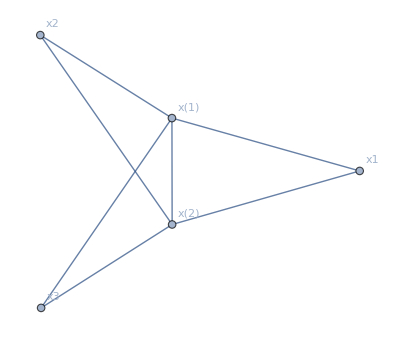
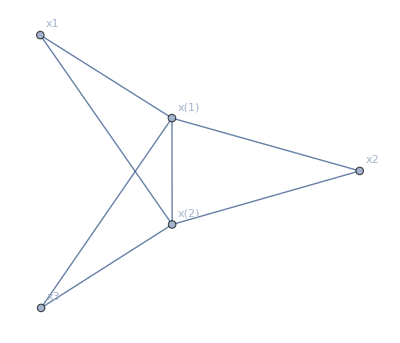
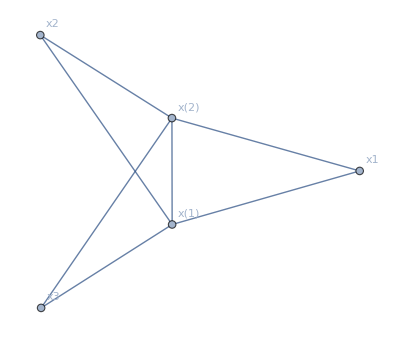
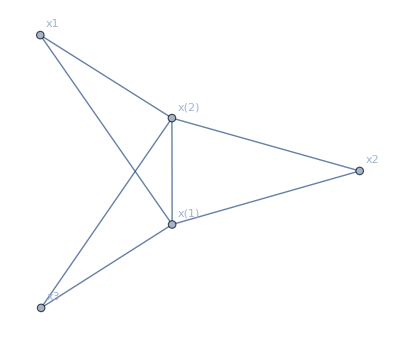
-2^(2-N) (-Graphics-+-Graphics-+-Graphics-+-Graphics-) N^-N π^4 ξ^4 N! II[{x1,x2}]^(-2+N) II[{x1,x[1]}] II[{x1,x[2]}] II[{x2,x[1]}] II[{x2,x[2]}] II[{x3,x[1]}] II[{x3,x[2]}] II[{x[1],x[2]}] u_(ϕ1 ϕ2)^(-2+N) u_(X X̄)^4 u_(Z Z̄)^3

-2^(4-N) N^-N π^4 ξ^4 N! II[{x1,x2}]^(-2+N) II[{x1,x[1]}] II[{x1,x[2]}] II[{x2,x[1]}] II[{x2,x[2]}] II[{x3,x[1]}] II[{x3,x[2]}] II[{x[1],x[2]}] u_(ϕ1 ϕ2)^(-2+N) u_(X X̄)^4 u_(Z Z̄)^3

```mathematica
Lp=4;
V=2;
max1OverN=∞;
A=.;
B=.;
doubleTraceVertices=True;

scalartype={X̄+Z,X̄+Z̄};
singletrace={Subscript[X[x3], o[1],o[2]],Subscript[X[x3], o[2],o[1]]};
```

True

True

non-zero

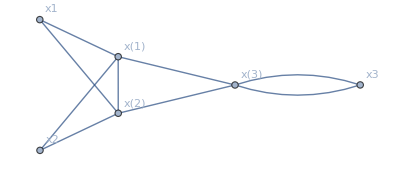
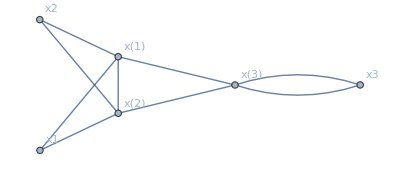
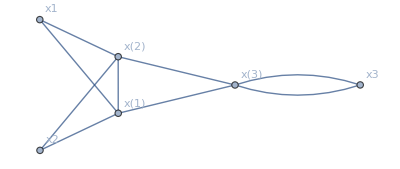
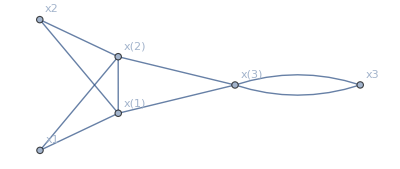
2^(5-N) (-Graphics-+-Graphics-+-Graphics-+-Graphics-) N^-N π^6 α1^2 ξ^4 N! II[{x1,x2}]^(-2+N) II[{x1,x[1]}] II[{x1,x[2]}] II[{x2,x[1]}] II[{x2,x[2]}] II[{x3,x[3]}]^2 II[{x[1],x[2]}] II[{x[1],x[3]}] II[{x[2],x[3]}] u_(ϕ1 ϕ2)^(-2+N) u_(X X̄)^6 u_(Z Z̄)^3

2^(7-N) N^-N π^6 α1^2 ξ^4 N! II[{x1,x2}]^(-2+N) II[{x1,x[1]}] II[{x1,x[2]}] II[{x2,x[1]}] II[{x2,x[2]}] II[{x3,x[3]}]^2 II[{x[1],x[2]}] II[{x[1],x[3]}] II[{x[2],x[3]}] u_(ϕ1 ϕ2)^(-2+N) u_(X X̄)^6 u_(Z Z̄)^3

```mathematica
Lp=4;
V=3;
max1OverN=2;
A=.;
B=0;
doubleTraceVertices=True;

scalartype={X̄+Z,X̄+Z̄};
singletrace={Subscript[X[x3], o[1],o[2]],Subscript[X[x3], o[2],o[1]]};
```

```mathematica
Lp=6;
V=1;
max1OverN=2;
A=.;
B=0;
doubleTraceVertices=True;

scalartype={X̄+Z,X̄+Z̄};
singletrace={Subscript[X[x3], o[1],o[2]],Subscript[X[x3], o[2],o[1]]};
```

True

True

non-zero

0

0

```mathematica
Lp=6;
V=2;
max1OverN=2;
A=.;
B=0;
doubleTraceVertices=True;

scalartype={X̄+Z,X̄+Z̄};
singletrace={Subscript[X[x3], o[1],o[2]],Subscript[X[x3], o[2],o[1]]};
```

True

True

non-zero

0

0

True

True

non-zero

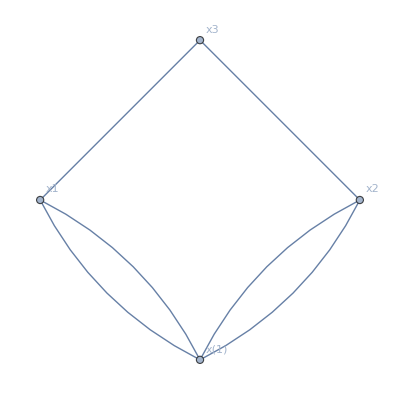
2^(1-N) -Graphics- N^-N π^2 (α2^2-ξ^2) N! II[{x1,x2}]^(-3+N) II[{x1,x3}] II[{x1,x[1]}]^2 II[{x2,x3}] II[{x2,x[1]}]^2 u_(ϕ1 ϕ2)^(-3+N) u_(X X̄)^4 u_(Z Z̄)^2

2^(1-N) N^-N π^2 (α2^2-ξ^2) N! II[{x1,x2}]^(-3+N) II[{x1,x3}] II[{x1,x[1]}]^2 II[{x2,x3}] II[{x2,x[1]}]^2 u_(ϕ1 ϕ2)^(-3+N) u_(X X̄)^4 u_(Z Z̄)^2

```mathematica
Lp=6;
V=1;
max1OverN=∞;
A=0;
B=0;
doubleTraceVertices=True;

scalartype={X+Z,X̄+Z̄};

singletrace={Subscript[X[x3], o[1],o[2]],Subscript[X̄[x3], o[2],o[1]]};
```

True

True

non-zero

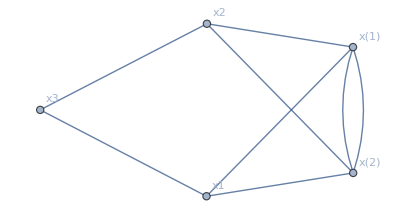
2^(3-N) -Graphics- N^-N π^4 (α2^2-ξ^2)^2 N! II[{x1,x2}]^(-3+N) II[{x1,x3}] II[{x1,x[1]}] II[{x1,x[2]}] II[{x2,x3}] II[{x2,x[1]}] II[{x2,x[2]}] II[{x[1],x[2]}]^2 u_(ϕ1 ϕ2)^(-3+N) u_(X X̄)^5 u_(Z Z̄)^3

2^(3-N) N^-N π^4 (α2^2-ξ^2)^2 N! II[{x1,x2}]^(-3+N) II[{x1,x3}] II[{x1,x[1]}] II[{x1,x[2]}] II[{x2,x3}] II[{x2,x[1]}] II[{x2,x[2]}] II[{x[1],x[2]}]^2 u_(ϕ1 ϕ2)^(-3+N) u_(X X̄)^5 u_(Z Z̄)^3

```mathematica
Lp=6;
V=2;
max1OverN=∞;
A=0;
B=0;
doubleTraceVertices=True;

scalartype={X+Z,X̄+Z̄};

singletrace={Subscript[X[x3], o[1],o[2]],Subscript[X̄[x3], o[2],o[1]]};
```

```mathematica
Lp=6;
V=1;
max1OverN=∞;
A=0;
B=0;
doubleTraceVertices=True;

scalartype={X+Z,X̄+Z̄};

singletrace={Subscript[X[x3], o[1],o[2]],Subscript[Z̄[x3], o[2],o[1]]};
```

True

True

non-zero

2^(1-N) -Graphics- N^-N π^2 (α2^2-ξ^2) N! II[{x1,x2}]^(-3+N) II[{x1,x3}] II[{x1,x[1]}]^2 II[{x2,x3}] II[{x2,x[1]}]^2 u_(ϕ1 ϕ2)^(-3+N) u_(X X̄)^3 u_(Z Z̄)^3

2^(1-N) N^-N π^2 (α2^2-ξ^2) N! II[{x1,x2}]^(-3+N) II[{x1,x3}] II[{x1,x[1]}]^2 II[{x2,x3}] II[{x2,x[1]}]^2 u_(ϕ1 ϕ2)^(-3+N) u_(X X̄)^3 u_(Z Z̄)^3

True

True

non-zero

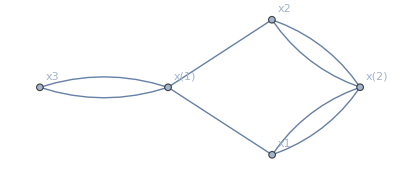
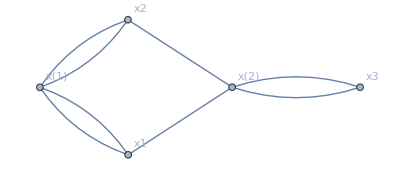
2^(2-N) N^-N π^4 (α2^2-ξ^2)^2 N! II[{x1,x2}]^(-3+N) II[{x1,x[1]}] II[{x1,x[2]}] II[{x2,x[1]}] II[{x2,x[2]}] (-Graphics- II[{x1,x[2]}] II[{x2,x[2]}] II[{x3,x[1]}]^2+-Graphics- II[{x1,x[1]}] II[{x2,x[1]}] II[{x3,x[2]}]^2+2 -Graphics- II[{x1,x3}] II[{x2,x3}] II[{x[1],x[2]}]^2) u_(ϕ1 ϕ2)^(-3+N) u_(X X̄)^4 u_(Z Z̄)^4

2^(2-N) N^-N π^4 (α2^2-ξ^2)^2 N! II[{x1,x2}]^(-3+N) II[{x1,x[1]}] II[{x1,x[2]}] II[{x2,x[1]}] II[{x2,x[2]}] (II[{x1,x[2]}] II[{x2,x[2]}] II[{x3,x[1]}]^2+II[{x1,x[1]}] II[{x2,x[1]}] II[{x3,x[2]}]^2+2 II[{x1,x3}] II[{x2,x3}] II[{x[1],x[2]}]^2) u_(ϕ1 ϕ2)^(-3+N) u_(X X̄)^4 u_(Z Z̄)^4

```mathematica
Lp=6;
V=2;
max1OverN=∞;
A=0;
B=0;
doubleTraceVertices=True;

scalartype={X+Z,X̄+Z̄};

singletrace={Subscript[X[x3], o[1],o[2]],Subscript[Z̄[x3], o[2],o[1]]};
```

# <tr(...) tr(...)>

True

True

non-zero

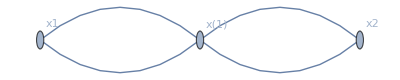
-4 -Graphics- π^2 α1^2 II[{x1,x[1]}]^2 II[{x2,x[1]}]^2 u_(X X̄)^4

-4 π^2 α1^2 II[{x1,x[1]}]^2 II[{x2,x[1]}]^2 u_(X X̄)^4

```mathematica
propagator=propagatorStandard;

V=1;
max1OverN=∞;
doubleTraceVertices=True;

singletrace1=contractionFreeHold[{Subscript[X[x1], o[1],o[2]],Subscript[X[x1], o[2],o[3]],Subscript[X[x1], o[3],o[4]],Subscript[Z[x1], o[4],o[1]]}];
singletrace2=contractionFreeHold[{Subscript[Z̄[x2], o[5],o[6]],Subscript[X̄[x2], o[6],o[7]],Subscript[X̄[x2], o[7],o[8]],Subscript[X̄[x2], o[8],o[5]]}];

singletrace1=(pm+1/4 ξ^2)contractionFreeHold[{Subscript[X[x1], o[1],o[2]],Subscript[X[x1], o[2],o[3]],Subscript[Z[x1], o[3],o[4]],Subscript[Z[x1], o[4],o[1]]}]+contractionFreeHold[{Subscript[X[x1], o[1],o[2]],Subscript[Z[x1], o[2],o[3]],Subscript[X[x1], o[3],o[4]],Subscript[Z[x1], o[4],o[1]]}];
singletrace2=(pm+1/4 ξ^2)contractionFreeHold[{Subscript[Z̄[x2], o[5],o[6]],Subscript[Z̄[x2], o[6],o[7]],Subscript[X̄[x2], o[7],o[8]],Subscript[X̄[x2], o[8],o[5]]}]+contractionFreeHold[{Subscript[Z̄[x2], o[5],o[6]],Subscript[X̄[x2], o[6],o[7]],Subscript[Z̄[x2], o[7],o[8]],Subscript[X̄[x2], o[8],o[5]]}];

singletrace1=contractionFreeHold[{Subscript[X[x1], o[1],o[2]],Subscript[Z[x1], o[2],o[3]],Subscript[Z[x1], o[3],o[4]],Subscript[Z[x1], o[4],o[1]]}];
singletrace2=contractionFreeHold[{Subscript[Z̄[x2], o[5],o[6]],Subscript[Z̄[x2], o[6],o[7]],Subscript[Z̄[x2], o[7],o[8]],Subscript[X̄[x2], o[8],o[5]]}];

singletrace1=contractionFreeHold[{Subscript[X[x1], o[1],o[2]],Subscript[X[x1], o[2],o[1]]}];
singletrace2=contractionFreeHold[{Subscript[X̄[x2], o[5],o[6]],Subscript[X̄[x2], o[6],o[5]]}];

(V≥0)&&(max1OverN≥0)

(* multiply traces *)
singletrace1 singletrace2//Expand;
(* one contractionFreeHold per addend *)
%//.{contractionFreeHold[list1_]contractionFreeHold[list2_]:>contractionFreeHold[Join[list1,list2]]};

(* insert vertices *)
%/.{contractionFreeHold[list_]:>If[(Count[(list//.{Subscript[ϕ_[x_], i_,j_]:>ϕ,Subscript[ϕ_[x[n_]], i_,j_]:>ϕ}),Z]==Count[(list//.{Subscript[ϕ_[x_], i_,j_]:>ϕ,Subscript[ϕ_[x[n_]], i_,j_]:>ϕ}),Z̄])&&(Count[(list//.{Subscript[ϕ_[x_], i_,j_]:>ϕ,Subscript[ϕ_[x[n_]], i_,j_]:>ϕ}),X]==Count[(list//.{Subscript[ϕ_[x_], i_,j_]:>ϕ,Subscript[ϕ_[x[n_]], i_,j_]:>ϕ}),X̄]),contractionFreeHold2[list],0]};
%/.{contractionFreeHold2[list_]:>vertexX[V,doubleTraceVertices]contractionFreeHold[list]}//Expand;
(* one contractionFreeHold per addend *)
%//.{contractionFreeHold[list1_]contractionFreeHold[list2_]:>contractionFreeHold[Join[list1,list2]]};

(* split into products of Z,Z̄ and products of X,X̄ *)
%//.{contractionFreeHold[list_]:>contractionFreeHold[Cases[list,Subscript[X[x__], i__,j__]],Cases[list,Subscript[X̄[x__], i__,j__]],Cases[list,Subscript[Z[x__], i__,j__]],Cases[list,Subscript[Z̄[x__], i__,j__]]]};

(* Wick contractions *)
If[V==0,tmp={%},tmp=List@@%];
Total[tmp]==%%//Expand

Monitor[
Table[tmp[[indexSum]]=(tmp[[indexSum]]//.{contractionFreeHold[list1_,list2_,list3_,list4_]:>contractionFree[list1,list2,list3,list4,max1OverN]}),{indexSum,Length[tmp]}];
,Row[{ProgressIndicator[indexSum,{1,Length[tmp]}],indexSum,"/",Length[tmp]},""]];
tmp=Total[tmp];

If[tmp===0,Print["zero"],Print["non-zero"]];
Series[tmp,{N,∞,0}]//Normal;
%//PowerExpand//Expand;
%/.{graphSpacetime[list_]:>Graph[list,VertexLabels->"Name"]}//Simplify
%%/.{graphSpacetime[list_]:>1}//Simplify//Expand

Clear[V,max1OverN,doubleTraceVertices,singletrace1,singletrace2,propagator,tmp,indexSum]
```